```mathematica
m = {{(σ + 1) , 3}, {-2 , (σ - 1)}}
```

{{1+σ,3},{-2,-1+σ}}

```mathematica
λ = Eigenvalues[m]
```

{-ⅈ √5+σ,ⅈ √5+σ}

```mathematica
V = Eigenvectors[m]
```

{{1/2 (-1+ⅈ √5),1},{1/2 (-1-ⅈ √5),1}}

```mathematica
Cs= Solve[C1*V[[1]]+C2*V[[2]]=={u,v},{C1,C2}]
```

{{C1→-1/10 ⅈ (2 √5 u+5 ⅈ v+√5 v),C2→1/10 ⅈ (2 √5 u-5 ⅈ v+√5 v)}}

```mathematica
c1  = Cs[[1]][[1]][[2]]
```

-1/10 ⅈ (2 √5 u+5 ⅈ v+√5 v)

```mathematica
c2 = Cs[[1]][[2]][[2]]
```

1/10 ⅈ (2 √5 u-5 ⅈ v+√5 v)

```mathematica
S=c1*Exp[λ[[1]]*t]*V[[1]]+c2*Exp[λ[[2]]*t]*V[[2]]
```

{1/20 ⅈ (-1-ⅈ √5) ⅇ^(t (ⅈ √5+σ)) (2 √5 u-5 ⅈ v+√5 v)-1/20 ⅈ (-1+ⅈ √5) ⅇ^(t (-ⅈ √5+σ)) (2 √5 u+5 ⅈ v+√5 v),1/10 ⅈ ⅇ^(t (ⅈ √5+σ)) (2 √5 u-5 ⅈ v+√5 v)-1/10 ⅈ ⅇ^(t (-ⅈ √5+σ)) (2 √5 u+5 ⅈ v+√5 v)}

```mathematica
sol = Simplify[ComplexExpand[S]]
```

```mathematica
{1/5 ⅇ^(t σ) (5 u Cos[√5 t]+√5 (u+3 v) Sin[√5 t]),1/5 ⅇ^(t σ) (5 v Cos[√5 t]-√5 (2 u+v) Sin[√5 t])}
```

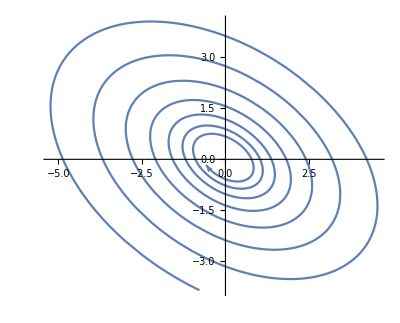

```mathematica
ParametricPlot[S/. {u->1,v->1,σ->-1/10},{t,-10,10}] /. Line[x_]:>{Arrowheads[{0.,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.}],Arrow[x]}
```

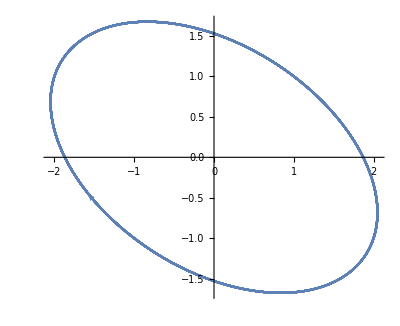

```mathematica
ParametricPlot[S/. {u->1,v->1,σ->0},{t,-10,10}] /.Line[x_]:>{Arrowheads[{0.,0.07,0.07,0.07,0.07,0.07,0.}],Arrow[x]}
```

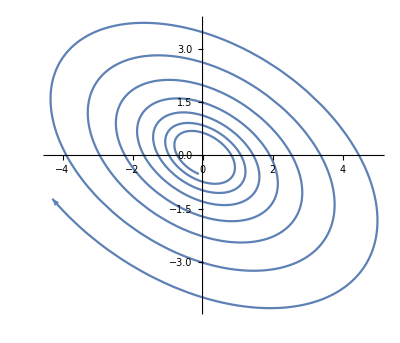

```mathematica
ParametricPlot[S/. {u->1,v->1,σ->1/10},{t,-10,10}] /. Line[x_]:>{Arrowheads[{0.,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.}],Arrow[x]}
```

```mathematica
max=FindMaximum[Norm[sol] /. {u->1,v->1, σ->0},t]
min=FindMinimum[Norm[S] /. {u->1,v->1,σ->0},t]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.25061,{t→0.637691}}

{1.39095,{t→1.34017}}

```mathematica
max/min
```

```mathematica
{1.6180339887498942,{(t->0.6376910210893485)/(t->1.3401724854932913)}}
```

{1.61803,{(t→0.637691)/(t→1.34017)}}

```mathematica
dir=S/. {u->1,v->1,σ->0,max[[2]][[1]]}
```

{1.91448+0. ⅈ,-1.18322+0. ⅈ}

```mathematica
Normalize[dir]
```

{0.850651+0. ⅈ,-0.525731+0. ⅈ}